4. dωmača nalogα, Diskretno modeliranje

### Besedilo

Imamo nalogo, v kateri želimo poiskati optimalno prirejanje tako, da bo skupni čas delavcev najmanjši. Imamo 25 delavcev in 20 opravil. Za vsako opravilo želimo dobiti delavca. Vsako opravilo lahko opravlja natanko en delavec. En delavec ne more opravljati več kot eno opravilo. Zato bo 5 delavcev ostalo brez opravila. Spodaj imamo matriko dimenzije mXn, ki nam podaja čas opravil, ki ga i-ti delavec porabi za j-to opravilo. Zanima nas, kolikšen je najmanjši skupni čas. Zanima nas tudi, kateri delavci bodo ostali brez dela.

```mathematica
(casOpravil = {{10,6,16,12,5,14,15,19,5,2,1,13,4,9,1,15,3,18,17,14},{14,4,5,9,8,3,10,6,20,13,17,15,9,16,9,14,4,7,8,17},{15,15,9,15,18,12,19,15,16,6,8,19,6,16,6,17,13,18,15,14},{11,8,17,3,7,17,10,3,12,17,5,6,7,16,3,11,12,2,5,17},{18,6,3,17,17,14,4,3,18,18,14,1,18,8,4,12,17,15,16,15},{13,19,1,1,20,10,4,15,10,5,3,16,4,18,11,6,10,14,8,13},{10,16,14,9,15,9,18,15,10,6,9,3,20,19,16,12,12,14,20,17},{15,6,19,20,3,4,8,14,8,7,18,4,5,20,6,6,8,17,10,18},{2,7,7,17,5,19,1,5,7,7,8,13,2,12,12,7,16,14,3,2},{8,11,1,20,10,14,2,10,20,4,11,19,18,1,11,19,17,5,19,20},{19,13,19,2,15,3,5,9,13,10,1,18,14,17,14,19,9,10,19,4},{14,5,9,19,19,13,10,10,12,15,5,17,4,8,5,5,7,14,18,3},{1,11,19,9,8,5,4,8,4,2,2,1,13,10,5,18,3,7,10,12},{11,12,13,18,17,20,15,17,9,4,8,11,17,5,12,12,8,5,3,19},{10,1,16,18,5,8,18,17,2,15,8,19,9,14,20,3,7,7,16,11},{20,8,1,2,17,19,1,19,9,18,17,20,9,14,19,9,8,16,6,3},{7,6,2,11,13,1,18,15,19,10,4,2,8,5,10,20,2,7,14,1},{14,3,20,12,18,4,4,11,10,7,12,11,18,1,10,1,16,9,20,10},{14,16,14,14,5,5,2,7,15,10,12,18,3,12,9,2,13,16,7,7},{13,6,14,10,20,4,15,16,2,7,9,10,16,5,15,11,8,10,20,17},{3,9,19,5,14,3,13,16,6,20,20,17,8,17,18,20,8,17,20,10},{12,6,19,17,13,9,9,12,12,15,12,9,4,2,8,14,4,6,4,17},{19,19,20,9,3,19,20,17,20,13,11,14,14,15,17,8,17,6,13,6},{7,3,9,8,16,15,20,6,19,9,9,9,18,8,1,2,11,13,15,20},{15,17,19,11,14,13,2,15,6,8,11,14,17,7,20,16,3,3,2,10}});
```

### Rešitev

```mathematica
{m,n} = Dimensions[casOpravil];
```

Označimo sedaj matriko prirejanj z X. Je istih dimenzij kot matrika s časi opravil. Na nek način je matrika prirejanj indikatorska matrika, ker bodo v njej nastopale le vrednosti 0 in 1. Vrednost 1 v matriki X na (i)(j)-tem mestu pomeni, da je delavec i dobil delo j, vrednos 0 pa, da dela ni dobil.

```mathematica
(X = Table[Subscript[x, i,j],{i,m},{j,n}])//MatrixForm;
```

#### Kriterijska funkcija

Ukaz Plus@@Flatten[mat*X] nam da kriterijsko funkcijo. Kriterijska funkcija je sestavljena iz tega, da vsak x_(i,j)∈{0,1}zmnožimo z istoležnim koeficientom v matriki časov opravil. Operator med členi je +.

```mathematica
kriterijskaFn = Plus@@Flatten[casOpravil*X];
```

#### Pogoji

Pogoj za delavce je, da vsak delavec opravlja največ eno delo. Računsko to pomeni, da je vsota vseh členov v eni vrstici matrike prirejanja največ ena. Lahko delavec tudi ne opravlja dela? Seveda, saj imamo 5 delavcev več kot je opravil. 
Pogoj za opravila je, da ima vsako opravilo natanko enega delavca, ki ga opravlja. Računsko to pomeni, da je vsota vseh členov v eni vrstici matrike prirejanja natanko enaka ena.
Dodamo še pogoj za nenegativnost.

```mathematica
pogojDelavci = Plus@@#≤1&/@X;
pogojOpravila = Plus@@#==1&/@Transpose[X];
pogojNenegativnost = #≥0&/@Flatten[X];
```

Želimo v čim krajšem skupnem času opraviti vsa opravila. Zato uporabimo Minimize na zgoraj navedeni kriterijski funkciji. Nato navedemo pogoje. Rešujemo za vse x_(i,j)v kriterijski matriki X. Rešujemo le za cela števila.

```mathematica
resitev = Minimize[Join[
{kriterijskaFn,
pogojDelavci,
pogojOpravila,
pogojNenegativnost}
],
Flatten[X],
Integers
];
```

#### Minimalni čas

```mathematica
First[resitev]
```

37

Minimalni skupni čas, v katerem delavci opravijo vseh 20 opravil, je 37 ur. Sedaj v prikažimo matriko prirejanj, ki nam pove, keteri delavci opravijo posamezno opravilo.

#### Matrika prirejanj

```mathematica
(prirejanje = X/.Last[resitev])//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

#### Graf prirejanj

Narišimo graf prirejanja med delavci in opravili. Označimo delavce z A in opravila z B.

```mathematica
vozlisca = Table[Subscript[A, i],{i,1,m}]∪Table[Subscript[B, j],{j,1,n}]∪{s,t}
```

{s,t,A_1,A_2,A_3,A_4,A_5,A_6,A_7,A_8,A_9,A_10,A_11,A_12,A_13,A_14,A_15,A_16,A_17,A_18,A_19,A_20,A_21,A_22,A_23,A_24,A_25,B_1,B_2,B_3,B_4,B_5,B_6,B_7,B_8,B_9,B_10,B_11,B_12,B_13,B_14,B_15,B_16,B_17,B_18,B_19,B_20}

```mathematica
povezave = Table[s->Subscript[A, i],{i,1,m}]∪(Subscript[B, #]->t&/@Range[n])∪(Subscript[A, #[[1]]]->Subscript[B, #[[2]]]&/@Position[prirejanje,1])
```

{s->A_1,s->A_2,s->A_3,s->A_4,s->A_5,s->A_6,s->A_7,s->A_8,s->A_9,s->A_10,s->A_11,s->A_12,s->A_13,s->A_14,s->A_15,s->A_16,s->A_17,s->A_18,s->A_19,s->A_20,s->A_21,s->A_22,s->A_23,s->A_24,s->A_25,A_1->B_10,A_2->B_6,A_4->B_18,A_5->B_8,A_6->B_4,A_8->B_5,A_9->B_13,A_10->B_3,A_11->B_11,A_13->B_12,A_15->B_2,A_16->B_7,A_17->B_20,A_18->B_14,A_19->B_16,A_20->B_9,A_21->B_1,A_22->B_17,A_24->B_15,A_25->B_19,B_1->t,B_2->t,B_3->t,B_4->t,B_5->t,B_6->t,B_7->t,B_8->t,B_9->t,B_10->t,B_11->t,B_12->t,B_13->t,B_14->t,B_15->t,B_16->t,B_17->t,B_18->t,B_19->t,B_20->t}

```mathematica
BipartiteGraphQ[g]
```

True

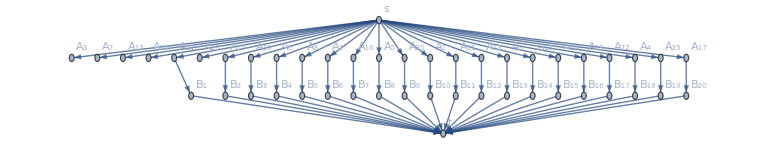

```mathematica
g = Graph[vozlisca,povezave,VertexLabels->"Name"]
```

Iz grafa razberemo, da so brez dela ostali delavci 3, 7, 12, 14 in 23. Graf je dvodelni.